```mathematica
WriteEdgesEnergies[DX_, DZ_, σE_,ϵ_, nameout_]:= Module[{rulesp, d,Energy, Final,nrg,Distance,Points,allp,alln, AllNeigh},
nrg[x_] :=RandomReal[NormalDistribution[ 0,σE]] +  (-27.21 * 0.529)/(ϵ x);

Distance[a_,  d_] := √(d^2((a⟦1⟧-Floor[DX/2])^2+(a⟦2⟧-Floor[DX/2])^2+(a⟦3⟧+1)^2));

Points[m_] := Tuples[{Range[0,DX-1],Range[0,DX-1],Range[0,m]}];
allp=Points[DZ];
rulesp = allp⟦#⟧-> #-1 &/@ Range[1, Length[allp]];
d=N[Distance[#,10]&/@ Points[DZ]];
Energy = nrg[#] &/@ d;
Export[ToString[nameout]<>"energies.txt", Energy];
AllNeigh[a_]:= Module[{Preprune}, 
Preprune={{Mod [a⟦1⟧+1,DX],a⟦2⟧,a⟦3⟧},
{Mod [a⟦1⟧-1,DX],a⟦2⟧,a⟦3⟧},
{a⟦1⟧,Mod[a⟦2⟧+1,DX],a⟦3⟧},
{a⟦1⟧,Mod[a⟦2⟧-1,DX],a⟦3⟧},
{a⟦1⟧,a⟦2⟧,a⟦3⟧-1},
{a⟦1⟧,a⟦2⟧,a⟦3⟧+1}};
Preprune= DeleteCases[Preprune /. {A_,B_,c_} /; c > DZ ||c<0-> "MEH" , "MEH"];
{a/.rulesp, #/.rulesp} &/@ Preprune
];
alln = AllNeigh[#]&/@allp;
Final = #/. {x__}-> x &/@ alln;
Final=Append[#, 0.05] &/@ Final;
Export[ToString[nameout]<>"edges.txt", Final, "Table"];
d
]
```

```mathematica
WriteEdgesEnergies[DX_, DZ_, σE_,ϵ_,F_,nameout_]:= Module[{rulesp, d,Energy, Final,nrg,Distance,Points,allp, AllNeigh,alln,RulesProps, Props},

Points[m_] := Tuples[{Range[0,DX-1],Range[0,DX-1],Range[0,m]}];
Distance[a_,  d_] := √(d^2((a⟦1⟧-Floor[DX/2])^2+(a⟦2⟧-Floor[DX/2])^2+(a⟦3⟧+1)^2));
RulesProps ={ {Floor[DX/2],Floor[DX/2],0} -> "Generator",{a_,b_, DZ}-> "Collector", {a_,b_,c_}-> "Nothing"};
nrg[x_] :=RandomReal[NormalDistribution[ 0,σE]] +  (-27.21 * 0.529)/(ϵ x) - F x;
allp=Points[DZ];
rulesp = allp⟦#⟧-> #-1 &/@ Range[1, Length[allp]];
d=N[Distance[#,10]&/@ Points[DZ]];
Energy = nrg[#] &/@ d;
Export[ToString[nameout]<>"energies.txt", Energy];
Props = allp/. RulesProps;
Export [ToString[nameout]<>"properties.txt",Props];
AllNeigh[a_]:= Module[{Preprune}, 
Preprune={{Mod [a⟦1⟧+1,DX],a⟦2⟧,a⟦3⟧},
{Mod [a⟦1⟧-1,DX],a⟦2⟧,a⟦3⟧},
{a⟦1⟧,Mod[a⟦2⟧+1,DX],a⟦3⟧},
{a⟦1⟧,Mod[a⟦2⟧-1,DX],a⟦3⟧},
{a⟦1⟧,a⟦2⟧,a⟦3⟧-1},
{a⟦1⟧,a⟦2⟧,a⟦3⟧+1}};
Preprune= DeleteCases[Preprune /. {A_,B_,c_} /; c > DZ ||c<0-> "MEH" , "MEH"];
{a/.rulesp, #/.rulesp} &/@ Preprune
];
alln = AllNeigh[#]&/@allp;
Final = #/. {x__}-> x &/@ alln;
Final=Append[#, 0.05] &/@ Final;
Export[ToString[nameout]<>"edges.txt", Final, "Table"];
d
]
```

```mathematica
Clear[WriteEdgesEnergiesNOPBC]

WriteEdgesEnergiesNOPBC[DX_, DZ_, σE_,ϵ_,F_,nameout_]:= WriteEdgesEnergiesNOPBC[DX, DZ, σE,ϵ,F,nameout,0.05, 0.001,1]
WriteEdgesEnergiesNOPBC[DX_, DZ_, σE_,ϵ_,F_,nameout_,trans_, CR_]:= WriteEdgesEnergiesNOPBC[DX, DZ, σE,ϵ,F,nameout,trans, CR,1]
WriteEdgesEnergiesNOPBC[DX_, DZ_, σE_,ϵ_,F_,nameout_,  trans_, CR_,start_]:= Module[{rulesp, d,Energy, Final,nrg,Distance,Points,allp, AllNeigh,alln, RulesProps, Props},

Points[m_] := Tuples[{Range[0,DX-1],Range[0,DX-1],Range[0,m-1]}];
Distance[a_,  d_] := √(d^2((a⟦1⟧-Floor[DX/2])^2+(a⟦2⟧-Floor[DX/2])^2+(a⟦3⟧+1)^2));
RulesProps ={ {Floor[DX/2],Floor[DX/2],start-1} -> "Generator",{a_,b_, DZ-1}-> "Collector", {a_,b_,c_}-> "Nothing"};
nrg[x_] :=RandomReal[NormalDistribution[ 0,σE]] +  (-27.21 * 0.529)/(ϵ x) - F x;
allp=Points[DZ];
rulesp = allp⟦#⟧-> #-1 &/@ Range[1, Length[allp]];
d=N[Distance[#,10]&/@ Points[DZ]];
Energy = nrg[#] &/@ d;
Props = allp/. RulesProps;

AllNeigh[a_]:= Module[{Preprune}, 
Preprune={{a⟦1⟧+1,a⟦2⟧,a⟦3⟧},
{a⟦1⟧-1,a⟦2⟧,a⟦3⟧},
{a⟦1⟧,a⟦2⟧+1,a⟦3⟧},
{a⟦1⟧,a⟦2⟧-1,a⟦3⟧},
{a⟦1⟧,a⟦2⟧,a⟦3⟧-1},
{a⟦1⟧,a⟦2⟧,a⟦3⟧+1}};
Preprune= DeleteCases[Preprune /. {A_,B_,c_} /; A<0 || A≥  DX || B<0 ||B≥ DX || c ≥ DZ ||c<0-> "MEH" , "MEH"];
{a/.rulesp, #/.rulesp} &/@ Preprune
];
alln = AllNeigh[#]&/@allp;
Final = #/. {x__}-> x &/@ alln;
Final=Append[#,  trans] &/@ Final;
Energy= Append[Energy, -1.0];
Props = Append[Props, "GroundState"];
Final = Append[Final,{Length[Energy]-1,{Floor[DX/2],Floor[DX/2],0} /. rulesp, CR}];
Final = Append[Final,{{Floor[DX/2],Floor[DX/2],0} /. rulesp,Length[Energy]-1, CR}];
Export[ToString[nameout]<>"edges.txt", Final, "Table"];
Export [ToString[nameout]<>"properties.txt",Props];
Export[ToString[nameout]<>"energies.txt", Energy];
Energy
]
WriteEdgesEnergiesNOPBC[DX_, DZ_, σE_,ϵ_,F_,nameout_,  trans_, CR_,start_,dmin_]:= Module[{rulesp, d,Energy, Final,nrg,Distance,Points,allp, AllNeigh,alln, RulesProps, Props},

Points[m_] := Tuples[{Range[0,DX-1],Range[0,DX-1],Range[0,m-1]}];
Distance[a_,  d_] := √(d^2((a⟦1⟧-Floor[DX/2])^2+(a⟦2⟧-Floor[DX/2])^2+(a⟦3⟧+dmin)^2));
RulesProps ={ {Floor[DX/2],Floor[DX/2],start-1} -> "Generator",{a_,b_, DZ-1}-> "Collector", {a_,b_,c_}-> "Nothing"};
nrg[x_] :=RandomReal[NormalDistribution[ 0,σE]] +  (-27.21 * 0.529)/(ϵ x) - F x;
allp=Points[DZ];
rulesp = allp⟦#⟧-> #-1 &/@ Range[1, Length[allp]];
d=N[Distance[#,10]&/@ Points[DZ]];
Energy = nrg[#] &/@ d;
Props = allp/. RulesProps;

AllNeigh[a_]:= Module[{Preprune}, 
Preprune={{a⟦1⟧+1,a⟦2⟧,a⟦3⟧},
{a⟦1⟧-1,a⟦2⟧,a⟦3⟧},
{a⟦1⟧,a⟦2⟧+1,a⟦3⟧},
{a⟦1⟧,a⟦2⟧-1,a⟦3⟧},
{a⟦1⟧,a⟦2⟧,a⟦3⟧-1},
{a⟦1⟧,a⟦2⟧,a⟦3⟧+1}};
Preprune= DeleteCases[Preprune /. {A_,B_,c_} /; A<0 || A≥  DX || B<0 ||B≥ DX || c ≥ DZ ||c<0-> "MEH" , "MEH"];
{a/.rulesp, #/.rulesp} &/@ Preprune
];
alln = AllNeigh[#]&/@allp;
Final = #/. {x__}-> x &/@ alln;
Final=Append[#,  trans] &/@ Final;
Energy= Append[Energy, -1.0];
Props = Append[Props, "GroundState"];
Final = Append[Final,{Length[Energy]-1,{Floor[DX/2],Floor[DX/2],0} /. rulesp, CR}];
Final = Append[Final,{{Floor[DX/2],Floor[DX/2],0} /. rulesp,Length[Energy]-1, CR}];
Export[ToString[nameout]<>"edges.txt", Final, "Table"];
Export [ToString[nameout]<>"properties.txt",Props];
Export[ToString[nameout]<>"energies.txt", Energy];
Energy
]
WriteEdgesEnergiesNOPBC[DX_, DZ_, σE_,ϵ1_,ϵ2_,F_,nameout_,  trans_, CR_,start_]:= Module[{rulesp, d,Energy, Final,nrg,Distance,Points,allp, AllNeigh,alln, RulesProps, Props},

Points[m_] := Tuples[{Range[0,DX-1],Range[0,DX-1],Range[0,m-1]}];
Distance[a_,  d_] := √(d^2((a⟦1⟧-Floor[DX/2])^2+(a⟦2⟧-Floor[DX/2])^2+(a⟦3⟧+1)^2));
RulesProps ={ {Floor[DX/2],Floor[DX/2],start-1} -> "Generator",{a_,b_, DZ-1}-> "Collector", {a_,b_,c_}-> "Nothing"};
nrg[{x1_, x2_}] :=RandomReal[NormalDistribution[ 0,σE]] +  (-27.21 * 0.529)/x2 2/(ϵ1+ϵ2)- F x2 + (27.21 * 0.529)/(2 x2 ϵ2) (ϵ2-ϵ1)/(ϵ1+ϵ2) ;
allp=Points[DZ];
rulesp = allp⟦#⟧-> #-1 &/@ Range[1, Length[allp]];
d=N[{#⟦3⟧*10+5,Distance[#,10]}&/@ Points[DZ]];
Energy = nrg[#] &/@ d;
Props = allp/. RulesProps;

AllNeigh[a_]:= Module[{Preprune}, 
Preprune={{a⟦1⟧+1,a⟦2⟧,a⟦3⟧},
{a⟦1⟧-1,a⟦2⟧,a⟦3⟧},
{a⟦1⟧,a⟦2⟧+1,a⟦3⟧},
{a⟦1⟧,a⟦2⟧-1,a⟦3⟧},
{a⟦1⟧,a⟦2⟧,a⟦3⟧-1},
{a⟦1⟧,a⟦2⟧,a⟦3⟧+1}};
Preprune= DeleteCases[Preprune /. {A_,B_,c_} /; A<0 || A≥  DX || B<0 ||B≥ DX || c ≥ DZ ||c<0-> "MEH" , "MEH"];
{a/.rulesp, #/.rulesp} &/@ Preprune
];
alln = AllNeigh[#]&/@allp;
Final = #/. {x__}-> x &/@ alln;
Final=Append[#,  trans] &/@ Final;
Energy= Append[Energy, -1.0];
Props = Append[Props, "GroundState"];
Final = Append[Final,{Length[Energy]-1,{Floor[DX/2],Floor[DX/2],0} /. rulesp, CR}];
Final = Append[Final,{{Floor[DX/2],Floor[DX/2],0} /. rulesp,Length[Energy]-1, CR}];
Export[ToString[nameout]<>"edges.txt", Final, "Table"];
Export [ToString[nameout]<>"properties.txt",Props];
Export[ToString[nameout]<>"energies.txt", Energy];
Energy
]
```

```mathematica
nrg= WriteEdgesEnergiesNOPBC[1,15,0.075,4, 0.001,  "5x5ran"<>ToString[#],0.05, 0.01,1]&/@Range[1,2];
```

```mathematica
nrg= WriteEdgesEnergiesNOPBC[5,5,0.075,4, 0.001,  "5x5ran"<>ToString[#],0.05, 0.01,1]&/@Range[1,2];
```

```mathematica
nrg= WriteEdgesEnergiesNOPBC[5,5,0.0000000000000001,3.0, 4, 0.001,  "5x5imagecrg2",0.05, 0.01,1];
```

```mathematica
nrg= WriteEdgesEnergiesNOPBC[5,5,0.0000000000000001,4., 4, 0.001,  "5x5noimagecrg",0.05, 0.01,1];
```

```mathematica
nrg= WriteEdgesEnergiesNOPBC[15,6,0.1,3, 0.001,  "15x6ran"<>ToString[#]];&/@Range[1,100]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
nrg= WriteEdgesEnergiesNOPBC[15,6,0.00000001,3, 0.001,  "15x6"];
```

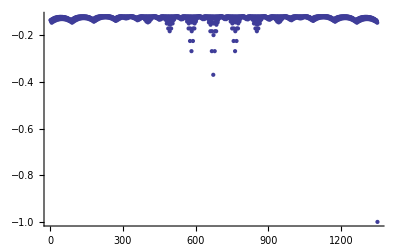

```mathematica
ListPlot[nrg, PlotRange-> All]
```

```mathematica
mv ..
```

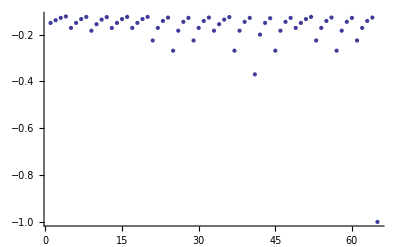

```mathematica
ListPlot[nrg, PlotRange-> All]
```

```mathematica
WriteEdgesEnergiesNOPBC[10,10,0.0001,4, 0.001*#,  "F"<>ToString[#]] &/@Range[0,10];
```

```mathematica
WriteEdgesEnergiesNOPBC[1,7,0.0001,3, 0.001 , "7x1"]
```

{-0.489713,-0.260069,-0.189807,-0.160058,-0.146162,-0.140148,-0.138625,-1.}

```mathematica
nrgan[x_] :=  - 1/(ϵ x)-F x
```

```mathematica
sol=Solve[D[nrgan[x],x]== 0 ,x]
```

{{x→-1/(√F √ϵ)},{x→1/(√F √ϵ)}}

```mathematica
sol /. {F-> 0.0010 , ϵ -> 3/(27.21 *0.529)}
```

{{x→-69.2678},{x→69.2678}}

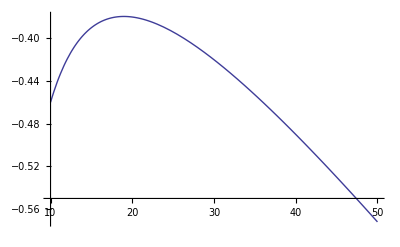

```mathematica
Plot[nrgan[x]/. {F-> 0.010 , ϵ -> 4/(27.21 *0.529)},{x,10,50}]
```

```mathematica
RulesJ ={};
avD = 5;
σD = 1;
d0=0.5;
Prefactor = a0 /. Solve[a0 Exp[-avD/d0]==0.05];
AddRandomJ[a_]:= Module[{J},
J =If [ Length[(a/. RulesJ )]== 2,Prefactor  Exp[-RandomReal[NormalDistribution[avD,σD]]/d0], a/.RulesJ];
RulesJ = If [ Length[(a/. RulesJ )]== 2,Append[RulesJ,a-> J], RulesJ];
RulesJ = If [ Length[(Reverse[a]/. RulesJ )]== 2,Append[RulesJ,Reverse[a]-> J], RulesJ];
Append[a,J]
]
```

```mathematica
(J /. RulesJ) == J
```

True

```mathematica
RulesJ
```

Rule[{2,1},0.0417906,Rule[{1,2},0.0417906,{}]]

```mathematica
AddRandomJ[{1,2}]
```

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

{1,2,0.0417906}

```mathematica
Onsager[parameters_] := Subscript[k, d]/(Subscript[k, d]+Subscript[k, f])/. Subscript[k, d]->  (3 μ e)/(4 Pi ϵ ϵ0 a^3)Exp[-ΔE/kT] (1+b+b^2/2+b^3/18)/. ΔE -> e/(4 π ϵ0 a ϵ)/. b-> (F e)/(8 Pi ϵ ϵ0 kT^2)/.{ϵ0 -> 8.85 10^-12, e -> 1.602176487 10^-19} //. parameters
```

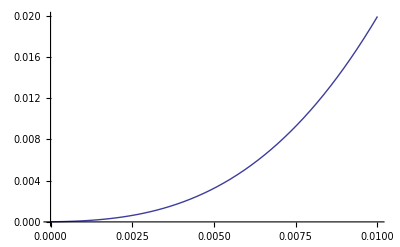

```mathematica
Plot[Onsager[{μ-> J^2/ℏ Exp[-λ/kT] a^2/kT √(Pi/(kT λ)), ϵ -> 4, kT -> 0.025, ΔE -> 0.36,a-> 10^-9, Subscript[k, f]-> 10^9, J-> 0.05, λ-> 0.3, ℏ -> 6.57×10^-16}] /. F -> 10^10 x ,{x, 0, 0.01 }]
```

```mathematica
J^2/ℏ/.{ ΔE -> 0.36,a-> 10^-9, Subscript[k, f]-> 10^9, J-> 0.05, λ-> 0.3, ℏ -> 6.57×10^-16}
```

3.80518×10^12

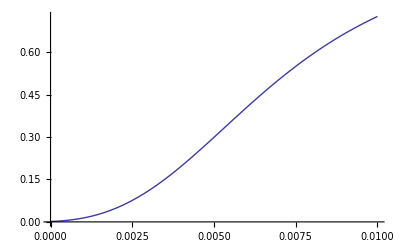

```mathematica
Plot[Onsager[{μ->10^-4, ϵ -> 4, kT -> 0.025,a-> 10^-9, Subscript[k, f]-> 4 10^10 }] /. F -> 10^10 x ,{x, 0, 0.01 }]
```

```mathematica
cd ..
```

```mathematica
μ//.{μ-> J^2/ℏ Exp[-λ/kT] a^2/kT √(Pi/(kT λ)), ϵ -> 4, kT -> 0.025, ΔE -> 0.36,a-> 10^-8, Subscript[k, f]-> 4 10^10, J-> 0.05, λ-> 0.2, ℏ -> 6.57×10^-16}
```

0.000127988

```mathematica
CoulombRadius[conditions_] := Solve[(-27.21 * 0.529)/(ϵ x) == -kT /. conditions,x];
```

```mathematica
CoulombRadius[{ϵ-> 4 , kT-> 0.025}]
```

{{x→143.941}}

```mathematica
Clear[WriteEdges1D]
WriteEdges1D[ DZ_,ϵ_,F_,kT_, nameout_]:= Module[{ d,Energy, Final,allp,alln1, alln2, Props},

allp=Range[0, DZ];
d=10 (#+1) &/@ allp;
Energy =  (-27.21 * 0.529)/(ϵ #) - F # - kT Log[3 (#/10)^2+3 #/10 +1] &/@ d;

alln1= {#,#+1, 0.05}&/@Range[0, DZ-1];
alln2 = {#,#-1, 0.05} &/@ Range[1,DZ]; 
Final = Join[alln1, alln2];
Energy= Append[Energy, -1.0];
Props =  "Nothing" &/@ Range[0, DZ+1];
Props⟦1⟧= "Generator";
Props⟦DZ+1⟧= "Collector";
Props⟦DZ+2⟧=  "GroundState";
Final = Append[Final, {0, Length[Energy]-1, 0.02}];
Final = Append[Final, {Length[Energy]-1,0, 0.02}];
Export[ToString[nameout]<>"edges.txt", Final, "Table"];
Export [ToString[nameout]<>"properties.txt",Props];
Export[ToString[nameout]<>"energies.txt", Energy];
Energy
]
```

```mathematica
WriteEdges1D[15, 4, 0.001 # , 0.025, "tmpF"<>ToString[#]] &/@ Range[0,10]
```

```mathematica
d=%;
```

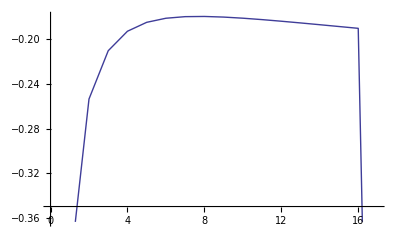
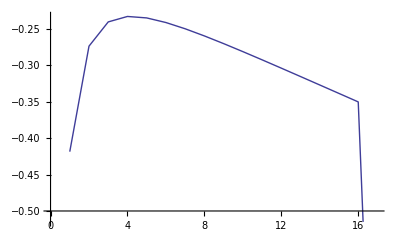
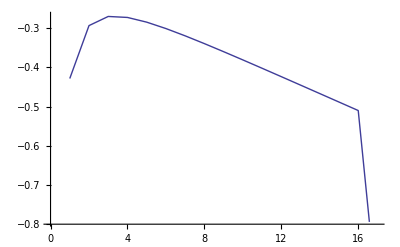
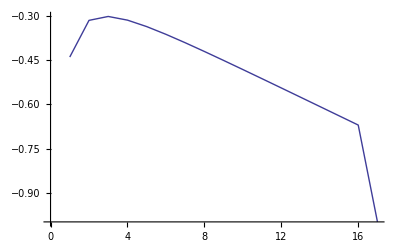
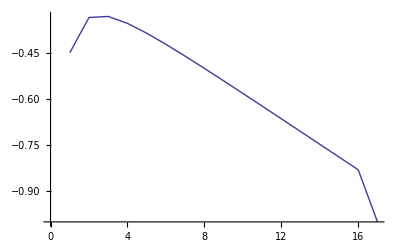
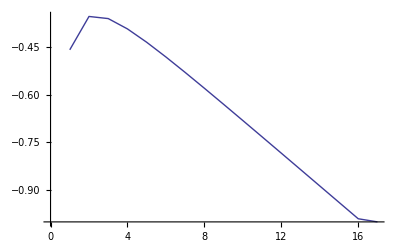
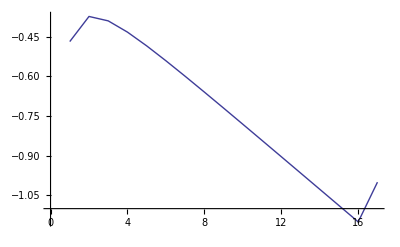
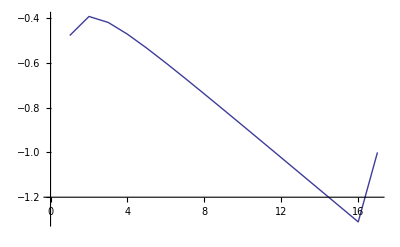

```mathematica
ListLinePlot[#] &/@ d
```

```mathematica
Clear[WriteEdges2carr]
WriteEdges2carr[DX_, DZ_, σE_,ϵ_,F_,nameout_]:= Module[{rulesp, d,Energy, Final,nrg,Distance,Points,allp, AllNeigh,alln, RulesProps, Props},

Points[m_] := Tuples[{Range[0,DX-1],Range[0,DX-1],Range[0,m]}];
Distance[a_,  b_,d_] := √(d^2((a⟦1⟧+b⟦1⟧)^2+(a⟦2⟧+b⟦2⟧)^2+(a⟦3⟧+b⟦3⟧+1)^2));
RulesProps ={ {{Floor[DX/2],Floor[DX/2],0},{Floor[DX/2],Floor[DX/2],0}} -> "Generator",{{a_,b_, DZ},{c_,d_, e_}}-> "Collector",{{c_,d_, e_},{a_,b_, DZ}}-> "Collector", {{a_,b_,c_},{d_,e_,f_}}-> "Nothing"};
nrg[x_] :=RandomReal[NormalDistribution[ 0,σE]] +  (-27.21 * 0.529)/(ϵ x) - F x;

Print["generate points"];
allp=Tuples[{Points[DZ],Points[DZ]}];

Print["generate rules"];
rulesp = allp⟦#⟧-> #-1 &/@ Range[1, Length[allp]];
d=N[Distance[#⟦1⟧,#⟦2⟧,10]&/@ allp];
Energy = nrg[#] &/@ d;
Props = allp/. RulesProps;

AllNeigh[a_,b_]:= Module[{Preprune}, 
Preprune={{{a⟦1⟧+1,a⟦2⟧,a⟦3⟧},b},
{{a⟦1⟧-1,a⟦2⟧,a⟦3⟧},b},
{{a⟦1⟧,a⟦2⟧+1,a⟦3⟧},b},
{{a⟦1⟧,a⟦2⟧-1,a⟦3⟧},b},
{{a⟦1⟧,a⟦2⟧,a⟦3⟧-1},b},
{{a⟦1⟧,a⟦2⟧,a⟦3⟧+1},b},
{a,{b⟦1⟧+1, b⟦2⟧, b⟦3⟧}},
{a,{b⟦1⟧-1, b⟦2⟧, b⟦3⟧}},
{a,{b⟦1⟧, b⟦2⟧+1, b⟦3⟧}},
{a,{b⟦1⟧, b⟦2⟧-1, b⟦3⟧}},
{a,{b⟦1⟧, b⟦2⟧, b⟦3⟧+1}},
{a,{b⟦1⟧, b⟦2⟧, b⟦3⟧-1}}};
Preprune= DeleteCases[Preprune /. {{A_,B_,c_} , {D_, E_, G_}}/; A<0 || A≥  DX || B<0 ||B≥ DX || c > DZ ||c<0-> "MEH" , "MEH"];
Preprune= DeleteCases[Preprune /. {{D_, E_, G_},{A_,B_,c_}  }/; A<0 || A≥  DX || B<0 ||B≥ DX || c > DZ ||c<0-> "MEH" , "MEH"];
{{a,b}/.rulesp, #/.rulesp} &/@ Preprune
];
Print["generate neighbour"];
alln = AllNeigh[#⟦1⟧,#⟦2⟧]&/@allp;
Final = #/. {x__}-> x &/@ alln;
Final=Append[#, 0.05] &/@ Final;
Energy= Append[Energy, -1.0];
Props = Append[Props, "GroundState"];
Final = Append[Final,{Length[Energy]-1,{{Floor[DX/2],Floor[DX/2],0},{Floor[DX/2],Floor[DX/2],0}}  /. rulesp, 0.02}];
Final = Append[Final,{{{Floor[DX/2],Floor[DX/2],0},{Floor[DX/2],Floor[DX/2],0}}  /. rulesp,Length[Energy]-1, 0.02}];
Export[ToString[nameout]<>"edges.txt", Final, "Table"];
Export [ToString[nameout]<>"properties.txt",Props];
Export[ToString[nameout]<>"energies.txt", Energy];
Energy
]
```

```mathematica
nrg =WriteEdges2carr[6,6, 0.001,3,0.001,"tmp"];
```

generate points

generate rules

generate neighbour

$Aborted

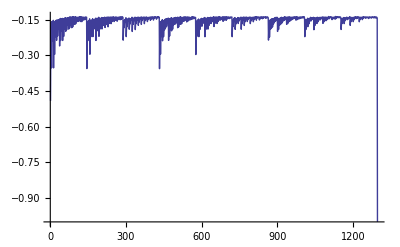

```mathematica
ListLinePlot[nrg, PlotRange-> All]
```

```mathematica
ℏ=6.57 10^-16
0.05^2/ℏ √(Pi/(0.1 0.025))
0.001^2/ℏ √(Pi/(0.1 0.025))
0.05^2/ℏ √(Pi/(0.05 0.025))
```

6.57×10^-16

1.3489×10^14

5.3956×10^10

1.90763×10^14